# Particle Diffusion

Michael Jones and Ian Jackson

```mathematica
Clear["`*"]
Needs["Units`"]
```

Start by creating a GUI window

```mathematica
DynamicModule[{f,p},f[g_]:=Graphics[g,ImageSize->Tiny];{SetterBar[Dynamic[p],{Disk[]->Disk,Rectangle[]->Rectangle}],Dynamic[f[p]]}]
```

2D draw path function

```mathematica
drawPath2D[a_,num_,c_,l_,w_]:=Module[{m,R,simR,σ,width,height,objectX,objectY,V,λ,collisions,pathLength,pathAngle,coordinates,index,newX,newY},
m=ElementData[atom,"AtomicMass"];
m=UnitConvert[m,"MeV/c^2"];
R=ElementData[a,"AtomicRadius"];
simR=QuantityMagnitude[R]/1000;
σ=Pi R^2;
width=Quantity[w,"um"];
height=Quantity[l,"um"];
objectX=width/2;
objectY=height/2;
V=width height (2 R);
n=num/V;
λ=1/(n σ);
collisions=c;
pathLength={};
Do[pathLength=Append[pathLength,λ+λ (-1)^RandomInteger[1] (E^(-RandomReal[{.25,4}]))],collisions];
pathAngle=RandomReal[2 Pi,collisions];
coordinates={{objectX,objectY}};
index=1;
Do[newX=coordinates[[index,1]]+pathLength[[index]] Cos[pathAngle[[index]]];
newY=coordinates[[index,2]]+pathLength[[index]] Sin[pathAngle[[index]]];
coordinates=Append[coordinates,{newX,newY}];
index++;,
collisions];
Graphics[{{Black,Line[QuantityMagnitude[UnitConvert[coordinates,"um"]]]},{Red,Line[{QuantityMagnitude[coordinates[[1]]],QuantityMagnitude[coordinates[[collisions+1]]]}]}},Frame->True,PlotRange->{{0,QuantityMagnitude[width]},{0,QuantityMagnitude[height]}}]
]
```

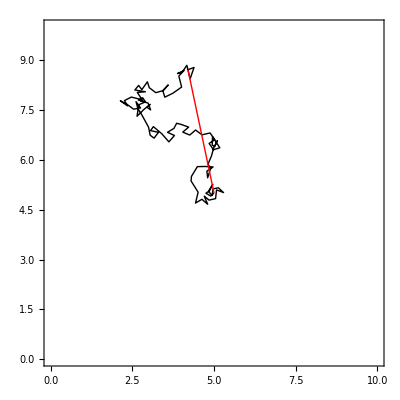

```mathematica
drawPath2D["Hydrogen",5000000,100,10,10]
```

3D draw path function

```mathematica
drawPath3D[a_,num_,c_,l_,w_,d_]:=Module[{m,R,simR,σ,width,height,depth,objectX,objectY,objectZ,V,λ,collisions,pathLength,pathAngle,pathAngleVert,coordinates,index,newX,newY,newZ,distance},
m=ElementData[atom,"AtomicMass"];
m=UnitConvert[m,"MeV/c^2"];
R=ElementData[a,"AtomicRadius"];
simR=QuantityMagnitude[R]/1000;
σ=Pi R^2;
width=Quantity[w,"um"];
height=Quantity[l,"um"];
depth=Quantity[d,"um"];
objectX=width/2;
objectY=height/2;
objectZ=depth/2;
V=width height (2 R);
n=num/V;
λ=1/(n σ);
collisions=c;
pathLength={};
Do[pathLength=Append[pathLength,λ+λ (-1)^RandomInteger[1] (E^(-RandomReal[{.25,4}]))],collisions];
pathAngle=RandomReal[2 Pi,collisions];
pathAngleVert=RandomReal[{-Pi/2,Pi/2},collisions];
coordinates={{objectX,objectY,objectZ}};
index=1;
Do[newX=coordinates[[index,1]]+pathLength[[index]] Cos[pathAngleVert[[index]]] Cos[pathAngle[[index]]];
newY=coordinates[[index,2]]+pathLength[[index]] Cos[pathAngleVert[[index]]] Sin[pathAngle[[index]]];
newZ=coordinates[[index,3]]+pathLength[[index]] Sin[pathAngleVert[[index]]];
coordinates=Append[coordinates,{newX,newY,newZ}];
index++;,
collisions];
distance=EuclideanDistance[coordinates[[1]],coordinates[[collisions+1]]];
{Graphics3D[{{Black,Line[QuantityMagnitude[UnitConvert[coordinates,"um"]]]},{Red,Line[{QuantityMagnitude[coordinates[[1]]],QuantityMagnitude[coordinates[[collisions+1]]]}]}},PlotRange->{{0,QuantityMagnitude[width]},{0,QuantityMagnitude[height]},{0,QuantityMagnitude[depth]}}],distance}
]
```

```mathematica
{plot,distance}=drawPath3D["Hydrogen",5000000,300,10,10,10];
plot
distance
```

-Graphics3D-

3.79289 μm